## Show parametric uncertainties in Nyquist plot (Example 9.2)

```mathematica
Clear["Global`*"];
```

```mathematica
g=ComplexExpand[k/(1+ s)ⅇ^(-τ s)/.s->ⅈ ω];Reg=Simplify[Re[g],{k>0,τ>0,ω>0}]
```

(k (Cos[τ ω]-ω Sin[τ ω]))/(1+ω^2)

```mathematica
Img=Simplify[Im[g],{k>0,τ>0,ω>0}]
```

-(k (ω Cos[τ ω]+Sin[τ ω]))/(1+ω^2)

```mathematica
Reg0=Reg/.{k->1,τ->1}; Img0=Img/.{k->1,τ->1};
```

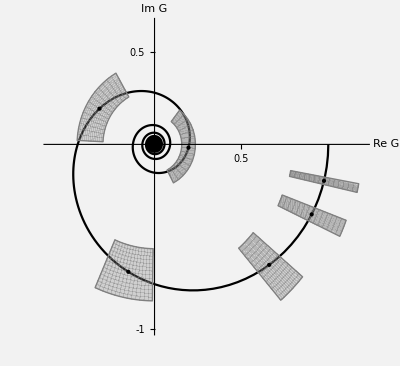

```mathematica
SetOptions[ParametricPlot,PlotRange->{{-0.6,1.2},{-1,0.65}},PlotStyle->Gray,BoundaryStyle->Gray,
BaseStyle->{FontFamily->"Gill Sans",FontSize->24},Ticks->{{{-0.5,},0.5,{1,}},{-1,{-0.5,},0.5}}];

p0=ParametricPlot[{Reg,Img}/.{k->1,τ->1},{ω,0,100},PlotStyle->Black];
p1=ParametricPlot[{Reg,Img}/.ω->0.1,{k,0.8,1.2},{τ,0.8,1.2}];
p2=ParametricPlot[{Reg,Img}/.ω->0.2,{k,0.8,1.2},{τ,0.8,1.2}];
p3=ParametricPlot[{Reg,Img}/.ω->0.4,{k,0.8,1.2},{τ,0.8,1.2}];
p4=ParametricPlot[{Reg,Img}/.ω->1,{k,0.8,1.2},{τ,0.8,1.2}];
p5=ParametricPlot[{Reg,Img}/.ω->2.5,{k,0.8,1.2},{τ,0.8,1.2}];
p6=ParametricPlot[{Reg,Img}/.ω->5,{k,0.8,1.2},{τ,0.8,1.2}];

p1a=Graphics[{PointSize[Large],Point[{Reg0,Img0}/.ω->0.1]}];
p2a=Graphics[{PointSize[Large],Point[{Reg0,Img0}/.ω->0.2]}];
p3a=Graphics[{PointSize[Large],Point[{Reg0,Img0}/.ω->0.4]}];
p4a=Graphics[{PointSize[Large],Point[{Reg0,Img0}/.ω->1.0]}];
p5a=Graphics[{PointSize[Large],Point[{Reg0,Img0}/.ω->2.5]}];
p6a=Graphics[{PointSize[Large],Point[{Reg0,Img0}/.ω->5.0]}];

p1b=Graphics[{Gray,Dashed,Circle[{Reg0,Img0}/.ω->0.1,0.2]}];
p2b=Graphics[{Gray,Dashed,Circle[{Reg0,Img0}/.ω->0.2,0.2]}];
p3b=Graphics[{Gray,Dashed,Circle[{Reg0,Img0}/.ω->0.4,0.2]}];
p4b=Graphics[{Gray,Dashed,Circle[{Reg0,Img0}/.ω->1.0,0.2]}];
p5b=Graphics[{Gray,Dashed,Circle[{Reg0,Img0}/.ω->2.5,0.2]}];
p6b=Graphics[{Gray,Dashed,Circle[{Reg0,Img0}/.ω->5.0,0.2]}];

p0a=ParametricPlot[{Reg,Img}/.{k->0.8,τ->1},{ω,0,100},PlotStyle->{Black,Thin}];
p0b=ParametricPlot[{Reg,Img}/.{k->1.2,τ->1},{ω,0,100},PlotStyle->{Black,Thin}];

pall1=Show[p0,p1,p2,p3,p4,p5,p6,p1a,p2a,p3a,p4a,p5a,p6a,Background->RGBColor[0.95,0.95,0.95],AxesLabel->{"Re G","Im G"},PlotLabel->None,LabelStyle->{GrayLevel[0]}]
```

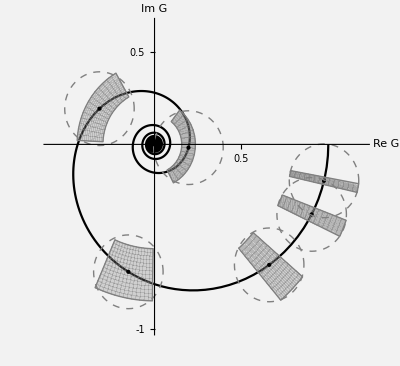

```mathematica
pall2=Show[p0,p1,p2,p3,p4,p5,p6,p1a,p2a,p3a,p4a,p5a,p6a,p1b,p2b,p3b,p4b,p5b,p6b,Background->RGBColor[0.95,0.95,0.95],AxesLabel->{"Re G","Im G"},PlotLabel->None,LabelStyle->{GrayLevel[0]}]
```

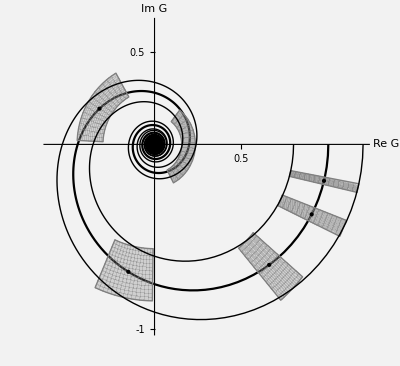

```mathematica
pall3=Show[p0,p1,p2,p3,p4,p5,p6,p1a,p2a,p3a,p4a,p5a,p0a,p0b,Background->RGBColor[0.95,0.95,0.95],AxesLabel->{"Re G","Im G"},PlotLabel->None,LabelStyle->{GrayLevel[0]}]
```

Export data

```mathematica
(* 
SetDirectory[NotebookDirectory[]];
Export["parametric1.pdf",pall1,"PDF"];
Export["parametric2.pdf",pall2,"PDF"];
Export["parametric3.pdf",pall3,"PDF"]; 
*)
```